Last modified on: Wednesday, July 11, 2018 at 9:07

Author Info

Luis Fernando Cantú Díaz de León

Carl Woll

Instituto Tecnológico Autónomo de México

Poster Session Content

Handwriting Recognition Using Neural Networks

The objective of this project, as the title implies, is to implement a neural network for handwriting recognition. This will be achieved using Connectionist Temporal Classification, an algorithm used for speech recognition and other sequence problems. If time allows, a secondary and optional objective will be to predict the character that follows the recognized characters.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

After training many Neural Networks, a Connectionist Temporal Classification (CTC) loss of 1.92 was achieved on the validation set. This could have possibly been lower with more computation time.

Create or work with a better dataset. IAM database has many errors and requires a lot of preprocessing.
Train a model on full sentences instead of words.
Form words with the characters of the EMNIST dataset and train a model on that data.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Problem

The problem to solve is easy to state:  What does the following image say?

-Graphics-

At first, this may seem as a trivial problem, but sometimes it is difficult for us to understand someone else’s handwriting. How difficult is it for a Neural Network?

Results

After training many Neural Networks, a Connectionist Temporal Classification (CTC) loss of 1.92 was achieved on the validation set. Despite several attempts, the results obtained using Convolutional and Recurrent Neural Networks were not satisfying. A main lesson was learned: Handwriting Recognition is not a simple a task because of its sequential nature.

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Despite several attempts, a satisfying result was not obtained. In the best model trained, a Connectionist Temporal Classification (CTC) loss of 1.92 was achieved on the validation set. 

The IAM Handwriting Database was the source of the images of handwritten words, but there were several problems that had to be dealt with.

There were already some issues during the collection of the data: several files were corrupt, and all of the images were of a different size. This meant that, in order to implement a model, much time was spent in the preprocessing of images of handwritten text. 

Besides the issue above, the image labels were also a problem, since many of the labels did not correspond to the text on the images. It was necessary to deal with this problems in order to prepare the data for the model.

#### Code

Most of the code written for this project had to do with image and string preprocessing. The following is one of the scripts I ran in an Amazon Web Services EC2 instance:

```mathematica
(*
The label data is read from the IAM database webpage. After reading the text file, some string processing
is done, since some of the labels have some errors and inconsistencies. 
*)
data = Import["http://www.fki.inf.unibe.ch/DBs/iamDB/data/ascii/words.txt"] // StringDrop[#,802]&;
dataTidy = StringReplace[data, "n log n"-> "nlogn"] // StringReplace[#, "B B C"-> "BBC"]& // StringReplace[#,"M P"-> "MP"]& // StringReplace[#, "A T V"-> "ATV"]&//StringReplace[#, "I T V"-> "ITV"]&//StringReplace[#,x:"NN "~~ "T V" :> x<>"TV"]& // StringReplace[#,"T C O" :> "T CO"]&;
dataList = (StringSplit[dataTidy]//Partition[#,9]& );
colNames = StringSplit@"word_id segmentation_result graylevel x_bounding y_bounding w_bounding h_bounding gramm_tag transcription"; 
dataSet = Association@@@Table[colNames[[i]]-> (dataList)[[j,i]], {j,1,Length[dataList]},{i,1,Length[colNames]}] // Dataset;

fileNames = FileNames["*.png",{"~/words"}, Infinity];

(* Some files are corrupt, so they are deleted. *)
newCol = Association["image"-> File@#]&/@fileNames;
dataSet = Join[dataSet, newCol,2 ] // Dataset;
dataSet = Delete[dataSet, {{4153},{113622}}];
fileNames =Delete[fileNames,{{4153},{113622}}];

(* This rectangle will be a white background for the images. *)
rectangle = Import["~/rectangle.png"];

(* Function used to fit an image to either width 128 or height 32, keeping aspect ratio. *)
reshape = Function[{image0, widthTarget0, heigthTarget0},
	Module[{image= image0,widthTarget = widthTarget0, heigthTarget=heigthTarget0, width, heigth ,fx,fy,f,newSize, resizedImage},
	{width,heigth} = ImageDimensions[image];
	fx=width/widthTarget;
	fy=heigth/heigthTarget;
	f=Max[fx,fy];
	newSize={Max[Min[widthTarget, Round[width/f]],1], Max[Min[heigthTarget,Round[heigth/f]],1]} ;
	resizedImage=ImageResize[image, newSize];
	resizedImage
	]
];

(* Function used to superimpose the image over the rectangle. *)
imageInRectangle = Function[{image0,rectangle0, widthTarget0, heigthTarget0},
	Module[{image=image0, rectangle=rectangle0,widthTarget = widthTarget0, heigthTarget=heigthTarget0, composedImage},
	composedImage=ImageCompose[rectangle, reshape[image,widthTarget, heigthTarget], {Center}];
	composedImage
	]
];

(*The next line has to be modified if running the script in Windows.*)
newDirectories5 = StringReplace[#,"/"~~LetterCharacter~~DigitCharacter..~~"-"~~DigitCharacter..~~LetterCharacter|""~~"-"~~DigitCharacter..~~"-"~~DigitCharacter..~~ ".png"-> ""]&/@fileNames // StringReplace[#,"/words"-> "/words_resized5"]&//DeleteDuplicates;

(*Uncomment the line below if you want to create the directories in your system.*)
(*CreateDirectory[File@#]&/@newDirectories5;*)

exportFileNames5 =StringReplace[#,"/words"-> "/words_resized5"]&/@fileNames;
```

```mathematica
(*
Uncomment and modify path if you want to export the files into a local directory.

ParallelMap[Export[exportFileNames5[[#]],ImageCompose[Import["~/rectangle.png"], reshape[Import@fileNames[[#]],128, 32], {Left,Center}, {Left, Center}]]&,Range[Length[fileNames]]]
*)
```

```mathematica
(* Further data preprocessing *)
imageAndLabels= dataSet[[1;;, {"image", "transcription"}]];
modifiedLabels=imageAndLabels[[1;;,2]]  // Normal;
modifiedImages=File[#]&/@exportFileNames5;
modifiedData = Table[modifiedImages[[n]]->  modifiedLabels[[n]], {n,1,Length[modifiedLabels],1}];
modifiedData = Select[modifiedData // Association, StringFreeQ[_?UpperCaseQ]] // Select[#, StringFreeQ[PunctuationCharacter]] & // Select[#, StringFreeQ[DigitCharacter]]& //Normal;

(* String with all characters (26 in total) *)
chars = Keys@KeySort@Counts@Flatten@Characters@modifiedData [[1;;,2]];

{testData, trainData} =  TakeDrop[modifiedData ,Ceiling[Length[dataSet]/10]];

encoder = NetEncoder[{"Image",{128,32}, "ColorSpace"-> "Grayscale"}];
decoder=NetDecoder[{"CTCBeamSearch",chars,"BeamSize"->50}];
ctcLoss = CTCLossLayer["Target"-> NetEncoder[{"Characters",chars}]];

(* One of the models *)
laNet2 = NetInitialize@NetChain[{
	ConvolutionLayer[64,{3,3}],
	Ramp,
	ConvolutionLayer[64,3],
	Ramp,
	PoolingLayer[2],
	ConvolutionLayer[128,3],
	Ramp,
	ConvolutionLayer[128,3],
	Ramp,
	PoolingLayer[2],
	ConvolutionLayer[256,3],
	Ramp,
	ConvolutionLayer[256,3],
	Ramp,
	ConvolutionLayer[512,3],
	Ramp,
	PoolingLayer[2],
	NetMapOperator@LinearLayer[Length[chars]+1],
	Ramp,
	DropoutLayer[0.5],
	NetMapOperator@LinearLayer[Length[chars]+1],
	DropoutLayer[0.5],
	SoftmaxLayer[]
	},
"Input"->encoder,
"Output"->decoder]
```

```mathematica
(* Training the model *)
laNet2Train = NetTrain[laNet2, trainData,LossFunction->ctcLoss,MaxTrainingRounds->50,ValidationSet->testData, TargetDevice->"GPU", TrainingProgressReporting-> "Print", TrainingProgressCheckpointing->{"Directory", "~/progress1", "Interval"-> Quantity[2,"Rounds"]}]

Export["~/net1.wlnet",laNet2Train]
```

#### Conclusions in Detail

Despite several attempts, the results obtained using Convolutional and Recurrent Neural Networks were not satisfying. A main lesson was learned: Handwriting Recognition is not a simple a task because of the sequential nature of it.

#### All Visualizations

Scatter plot of the width (x axis) and height (y axis) of all 115,318 images that were used for this project.

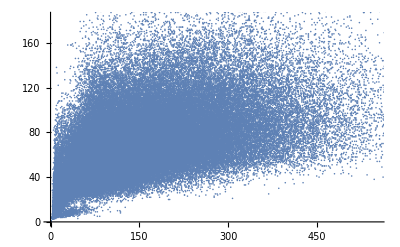

In the following histograms, we can see that the variability in both dimensions (top: width, down: height) was considerable, especially on the width, and this required some image preprocessing in order for the images to have the same size.

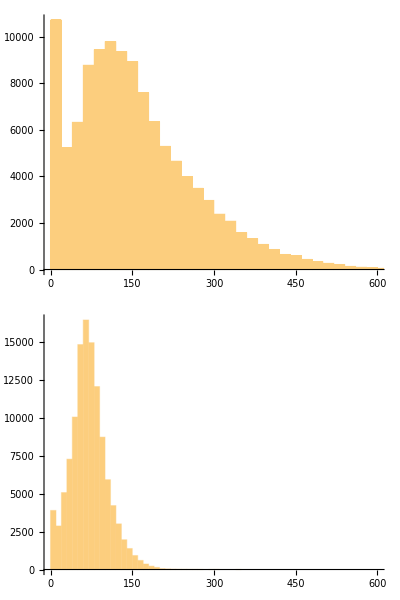

#### Data Sources Links/References

Data was obtained from the IAM Handwriting Database: http://www.fki.inf.unibe.ch/databases/iam-handwriting-database

#### Future Directions

Curate a better dataset.

Implement other kinds of networks to this problem (Densenet).

#### Background Info Links/References

U. Marti and H. Bunke. A full English sentence database for off-line handwriting recognition. In Proc. of the 5th Int. Conf. on Document Analysis and Recognition, pages 705 - 708, 1999.

S. Sudholt and G. A. Fink. PHOCNet: A Deep Convolutional Neural Network for Word Spotting in Handwritten Documents. Working Paper.

#### Keywords

Provide keywords as items

Neural Networks

Handwriting Recognition

Convolutional and Recurrent Neural Networks

#### Other information